Rigid Gyroscope x-y Plane Motion:

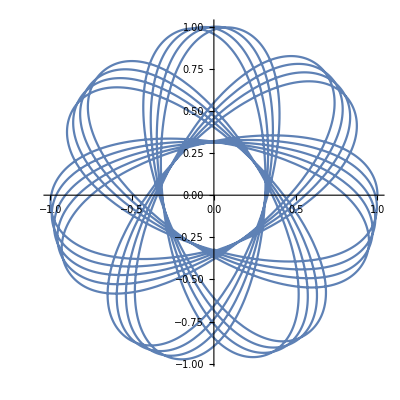

Rigid Gyroscope Motion:

```mathematica
m=1;
i=1;
l=1;
g=10;
Lx=y[t]pz[t]-z[t]py[t];
Ly=z[t]px[t]-x[t]pz[t];
Lz=x[t]py[t]-y[t]px[t];
ℋ=(Lx^2+Ly^2+Lz^2)/(2i)+m g z[t];
time=30;

eq1=x'[t]==D[ℋ,px[t]];
eq2=y'[t]==D[ℋ,py[t]];
eq3=z'[t]==D[ℋ,pz[t]];
eq4=px'[t]==-D[ℋ,x[t]];
eq5=py'[t]==-D[ℋ,y[t]];
eq6=pz'[t]==-D[ℋ,z[t]];

s=NDSolve[{eq1,eq2,eq3,eq4,eq5,eq6,x[0]==1,y[0]==0,z[0]==-1/2,px[0]==0,py[0]==1,pz[0]==0},{x,y,z,px,py,pz},{t,0,time},WorkingPrecision->20];

"Rigid Gyroscope x-y Plane Motion:"
ParametricPlot[Evaluate[{x[t],y[t]}/.s],{t,0,time},AspectRatio->1]

"Rigid Gyroscope Motion:"
R=3/2;
plt=Plot3D[-10l,{x,-R,R},{y,-R,R},PlotRange->{-R,R}];
Animate[Show[plt,Graphics3D[{Tube[{{0,0,0},{x[t],y[t],z[t]}},R/10]}],BoxRatios->Automatic,Ticks->None]/.s,{t,0,time},AnimationRate->1, AnimationRunning->False,RefreshRate->120]
```